```mathematica
ClearAll["Global`*"]
NotebookSave[]
Get["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Function_Garch.m"];
```

Set Parameters

```mathematica
Num=500;
M=50000;
callput="Put";
n=12;
T=1.;
Exporting=True;
Mail=False;
```

```mathematica
(*nums=Volatility["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\aapl.csv",5,n,T]*)(*(path, column in csv, number of exercise points, number of years) -> (final volatility, final stock price, a, b, w)*)
```

```mathematica
nums={0.5,171.1,0.05,0.9,0.3}
```

{0.5,171.1,0.05,0.9,0.3}

Distribution Parameters

```mathematica
rm=0.06;
rs=0.01;
sigmam=Max[nums[[1]],0.2];
sigmas=0.05;
S0m=nums[[2]];
S0s=sigmam;
a=nums[[3]];
b=nums[[4]];
w=Max[nums[[5]],0.2];
k=S0m*.9;
```

```mathematica
distrib={NormalDistribution[rm,rs],NormalDistribution[sigmam,sigmas],NormalDistribution[S0m,S0s]};
```

```mathematica
matrix=Table[distrib,{i,1,Num}];
```

```mathematica
MatRand1=Map[RandomVariate,matrix,{2}];
MatRand2=Map[RandomVariate,matrix,{2}];
```

```mathematica
(*Simul[M,callput,n,T,K,r,sigma,S0]*)
```

```mathematica
(*Param=Table[{M,callput,If[Mod[i-1,Num*3]≥Num*2,nm+ns,If[Mod[i-1,Num*3]≥Num,nm,nm-ns]],If[Mod[i-1,Num*9]≥Num*6,Tm+Ts,If[Mod[i-1,Num*9]≥Num*3,Tm,Tm-Ts]],
If[Mod[i-1,Num*27]≥Num*18,Km+Ks,If[Mod[i-1,Num*27]≥Num*9,Km,Km-Ks]]},{i,1,Num*27}];*)
```

```mathematica
Param=Table[{M,callput,n,T,k,a,b,w},{i,1,Num}];(*non-random parameters*)
```

```mathematica
MatA=Join[Param,MatRand1,2];
MatB=Join[Param,MatRand2,2];
```

```mathematica
For[i=Dimensions[Param][[2]]+1;VMat={},i≤Dimensions[MatA][[2]],i++,tmp=MatB;tmp[[All,i]]=MatA[[All,i]];AppendTo[VMat,tmp]]
```

```mathematica
DateList[]
```

{2017,11,21,1,26,9.2899333}

```mathematica
fA=ParallelTable[Simul@@MatA[[it3]],{it3,1,Num}];//AbsoluteTiming
```

{40795.4,Null}

```mathematica
If[Mail,txt="1st Matrix completed.\nDuration: "<>ToString[%[[1]]]<>"\nFinished at: "<>ToString[DateList[][[4]]]<>":"<>ToString[DateList[][[5]]];
SendMail["To"->"miguel.ribeiro.ist@gmail.com","Subject"->"Computation","Body"->txt],];
DateList[]
```

{2017,11,21,12,46,4.8924805}

```mathematica
fB=ParallelTable[Simul@@MatB[[it4]],{it4,1,Num}];//AbsoluteTiming
```

$Aborted

```mathematica
If[Mail,txt="2nd Matrix completed.\nDuration: "<>ToString[%[[1]]]<>"\nFinished at: "<>ToString[DateList[][[4]]]<>":"<>ToString[DateList[][[5]]];
SendMail["To"->"miguel.ribeiro.ist@gmail.com","Subject"->"Computation","Body"->txt],];
DateList[]
```

{2017,11,18,20,55,33.9541515}

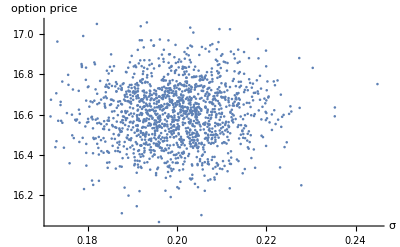

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

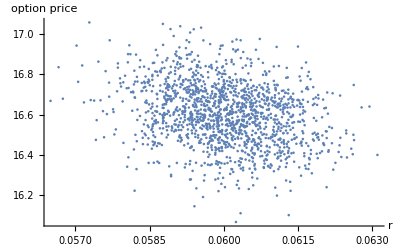

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

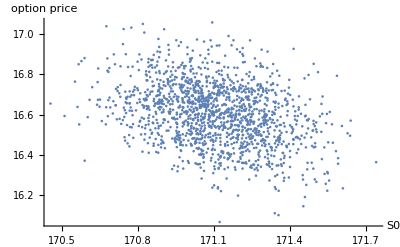

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
Monitor[For[it2=1;fVA={},it2<=Dimensions[VMat][[1]],it2++,tmp=ParallelTable[Simul@@VMat[[it2,it1]],{it1,1,Num}];AppendTo[fVA,tmp];If[Mail,txt=ToString[it2+2]<>
"th Secondary Matrix completed.\nFinished at: "<>ToString[DateList[][[4]]]<>":"<>ToString[DateList[][[5]]];
SendMail["To"->"miguel.ribeiro.ist@gmail.com","Subject"->"Computation","Body"->txt],]],ProgressIndicator[it2,{1,Dimensions[VMat][[1]]}]];//AbsoluteTiming
```

{23333.9,Null}

```mathematica
DateList[]
```

{2017,11,19,3,24,28.0991455}

```mathematica
(*For[x=1;Var={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fB[[w]]*(fVA[[x,w]]-fA[[w]]),{w,1,Num}];AppendTo[Var,tmp]]*)
```

```mathematica
For[x=1;Var1={},x≤Dimensions[fVA][[1]],x++,tmp=(1/Num*Sum[fA[[i]]*fVA[[x,i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2)/(1/Num*Sum[fA[[i]]*fA[[i]],{i,Num}]-(1/Num*Sum[fA[[i]],{i,Num}])^2);AppendTo[Var1,tmp]]
```

```mathematica
Var1
```

{-2.94302,8.05092,2.98914}

```mathematica
For[x=1;Var2={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Var2,tmp]]
```

```mathematica
Var2/Total[Var2,2]
```

{-3.08056,3.57168,0.508882}

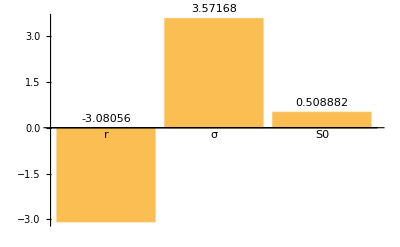

```mathematica
BarChart[Var2/Total[Var2,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

```mathematica
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA2.m",MatA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB2.m",MatB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA2.m",fA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB2.m",fB];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA2.m",fVA];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param2.m",Param[[1]]],];
```

```mathematica
If[Exporting,Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\sigma2.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}],"eps"];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\r2.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]];
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\S02.eps",ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}],"eps"],];
```

```mathematica
NotebookSave[]
```